```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gPlots3DEx`"];
Needs["gPlotsEx`"]; 
Needs["gBRDF`"];
Needs["gUtils`"];
Needs["pbrtShared`"];
Needs["pbrtLog`"];
SetDirectory[NotebookDirectory[]];

gPrint["Origin Scene"];
ClearAll[scene];
scene=pbrtLoadScene["pbrtTestScene.scene"];
Show[pbrtPlotOriginScene[scene],pbrtPlot3DOptions[scene]]
```

Origin Scene

-Graphics3D-

Rendered Scene

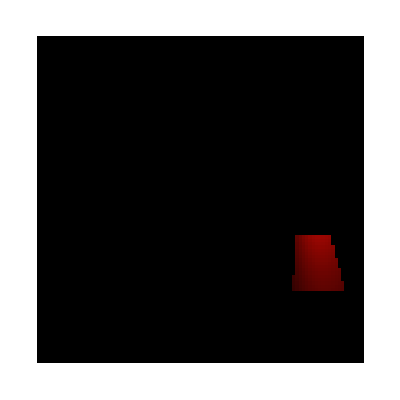

```mathematica
gPrint["Rendered Scene"];
ClearAll[scene,colorMul,imgTable];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul];
Show[ArrayPlot[imgTable]]
```

```mathematica
gPrint["Switch Scenes"];
ClearAll[scene,colorMul,imgTable,renderedFlag];
scene=pbrtLoadScene["pbrtTestScene.scene"];
colorMul=10;
imgTable=Table[1,scene["resx"],scene["resy"]];
renderedFlag=False;
Manipulate[
Show[
If[renderedFlag,
	ArrayPlot[imgTable],
	pbrtPlotOriginScene[scene]],

pbrtPlot3DOptions[scene]
],
Button["Rendered",renderedFlag=!renderedFlag],
Button["Start",imgTable=pbrtRenderTile[{77,61},{93,77},scene,colorMul]],
{{colorMul,10},1,20}
]
```

Switch Scenes

```mathematica
gPrint["Pixel Log"];
ClearAll[scene,l1,log1,l2,log2];
scene=pbrtLoadScene["pbrtTestScene.scene"];
l1=pbrtSamplerIntegratorRender[{51,12},scene];
log1=pbrtCurrPixelLog;
l2=pbrtSamplerIntegratorRender[{78,80},scene];
log2=pbrtCurrPixelLog;
pbrtLogPrintPixel[log1];
pbrtLogPrintPixel[log2];
```

Pixel Log

pixel

{51,12}

cameraRay

<|o→{278.,-800.,273.},d→{0.00986832,0.96904,0.246708}|>

li

{20.7467,10.8234,2.76459}

pixel

{78,80}

cameraRay

<|o→{278.,-800.,273.},d→{0.186158,0.96211,-0.199221}|>

li

{0.0737537,0.0302308,0.00738909}

```mathematica
gPrint["Validate Pixel"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateSinglePixel[51,12,scene,testData]
```

Validate Pixel

{True,{20.7467,10.8234,2.76459},{20.7467,10.8234,2.76459}}

```mathematica
gPrint["Validate Tile"];
ClearAll[scene,testData];
scene=pbrtLoadScene["pbrtTestScene.scene"];
testData=ToExpression[Import["pbrtTestData.pixels"]];
pbrtValidateTilePixels[{45,0},{61,13},scene,testData]
(*pbrtValidateTilePixels[{45,0},{46,1},scene,testData]*)
```

Validate Tile

<|total→208,ok→208,fail→0,black→193|>